```mathematica
f[h_]:=(Sqrt[2(-1.1723328*^18/(l+h)+1.1723328*^18/h)]/.l->13599840256)-Sqrt[1.1723328*^18/h]
```

```mathematica
f[68773560320]
```

-1756.23

```mathematica
vel[in_,th_,satevel_,GM_,close_,peri_]:=Block[{ink,z,result,result2,varth},
ink=Sqrt[in +GM/peri];
z=satevel Sin[th]-I(ink+satevel Cos[th]);varth =2ArcSin[1/(1+ink^2/GM*close)];result=Abs[z](Cos[Arg[z]+varth]+I Sin[Arg[z]+varth]);
result2=Abs[z](Cos[Arg[z]-varth]+I Sin[Arg[z]-varth]);{result+(-satevel Sin[th]+satevel Cos[th]),result2+(-satevel Sin[th]+satevel Cos[th])}]
```

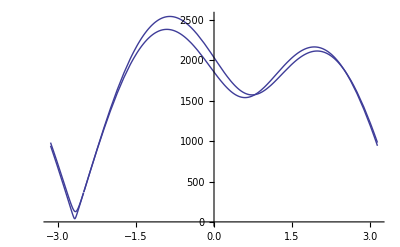

```mathematica
Plot[Abs[vel[845,x,945,8.1717302*^12,21000,14175000]],{x,-π,π}]
```

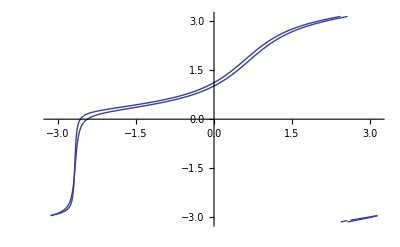

```mathematica
Plot[Arg[vel[845,x,945,8.1717302*^12,8000,14175000]],{x,-π,π}]
```

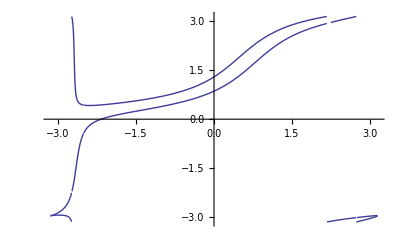

```mathematica
Plot[Arg[vel[826,x,945,8.1717302*^12,142570,14175000]],{x,-π,π}]
```

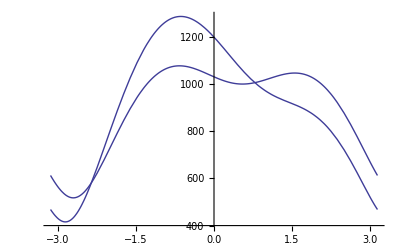

```mathematica
Plot[Abs[vel[826,x,314,8.1717302*^12,142570,14175000]],{x,-π,π}]
```

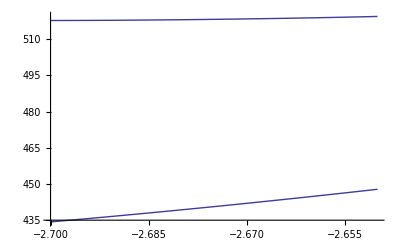

```mathematica
Plot[Abs[vel[826,x,314,8.1717302*^12,142570,14175000]],{x,-2.7,-2.65}]
```

```mathematica
Plot[Abs[vel[845,x,945,8.1717302*^12,8000,14175000]],{x,-π,π}]
```